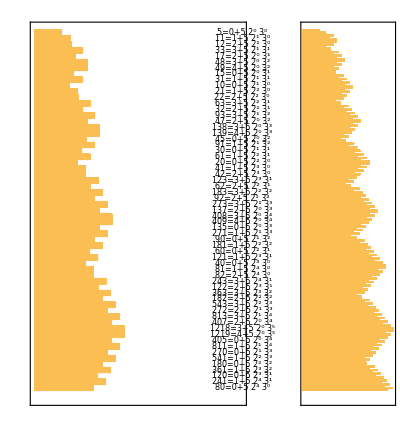

```mathematica
RMToAS[prog_,nr_]:=With[{p=Length[prog],g=∏_(j=1)^nr Prime[j]},{p g,Sort[Flatten[MapIndexed[With[{n=First[#2]-1},#1/.{i[r_]:>Table[n+j p->(Evaluate[Simplify[Prime[r] (#1-n)+n+1]]&),{j,0,g-1}],d[r_,k_]:>Table[n+j p->If[Mod[j,Prime[r]]==0,Evaluate[Simplify[(#1-n)/Prime[r]+k-1]]&,#1+1&],{j,0,g-1}]}]&,prog]]]}];

ASEvolveList[{n_,rules_},m_,t_]:=NestList[(Mod[#1,n]/.rules)[#1]&,m,t];

RMStep[prog_,state:{Halted,_List}]:=state;
RMStep[prog_,{instr_Integer,regs_List}]:=If[instr>Length[prog],{Halted,regs},With[{t=prog[[instr]]},If[Length[t]==1,{instr+1,MapAt[#1+1&,regs,First[t]]},If[regs[[First[t]]]==0,{instr+1,regs},{Last[t],MapAt[#1-1&,regs,First[t]]}]]]];

RMEvolveList[prog_,regs_,n_Integer]:=NestList[RMStep[prog,#]&,{1,regs},n];

RMGraphics[prog_List,history_]:=With[{states=history[[All,1]],regs=Transpose[history[[All,2]]]},GraphicsRow[{Graphics[MapIndexed[Disk[{#1,-First[#2]},.35]&,states],],,Splice[With[{gfun=Interpolation[{{1,.8},{Length[regs],.5}},InterpolationOrder->1]},MapIndexed[Graphics[{GrayLevel[gfun[First[#2]]],EdgeForm[Black],MapIndexed[Table[Rectangle[{i,-First[#2]}],{i,#}]&,#]},]&,regs]]]},Spacings->0]];

With[{rule={{1},{2,1},{2},{1,3},{2,1}}/.{{a_}->i[a],{a_,b_}->d[a,b]},decodestring=Function[{m,p,nr},DisplayForm[Style[RowBox[{m,"=",Mod[m,p],"+5",SuperscriptBox[2,#1],SuperscriptBox[3,#2]}],8,Italic,AutoMultiplicationSymbol->False,ScriptMinSize->1]]&@@(FactorInteger[Product[Prime[i],{i,2}]*Quotient[m,p]][[All,-1]]-1)]},GraphicsRow[{Show[{BarChart[Reverse@#,ScalingFunctions->{Log[10,#]&,#&},BarOrigin->Left,AspectRatio->1.6,Frame->True,FrameTicks->False,PlotRangePadding->{{0,Scaled[.15]},{-1.2,0}}],Graphics[Table[Text[decodestring[#[[i]],5,2],{7.5,Length[#]-i+1},{1,0}],{i,Length[#]}]]}]&@ASEvolveList[RMToAS[rule,2],5,60],BarChart[Reverse@#,ScalingFunctions->{Log[10,#]&,#&},BarOrigin->Left,AspectRatio->4,Frame->True,FrameTicks->False,PlotRangePadding->{{0,Scaled[.15]},{-1.2,0}},ChartStyle->EdgeForm[GrayLevel[.15]]]&@ASEvolveList[RMToAS[rule,2],5,200],RMGraphics[rule,RMEvolveList[rule,{0,0},60]]}]]
```